# Perturbation evolution in Matter-Radiation-(Dark Energy) Universe

We take into account here only the perturbations in CDM and photons.  You can change the initial conditions to study the evolution of the CDM isocurvature mode easily

## Universe composition

Universe composition

```mathematica
ΩΛ=0 (* 0.69 *)
Ωrad=0.9 10^-4
ΩM=1-ΩΛ-Ωrad
```

0

0.00009

0.99991

```mathematica
h=0.68
H0=100h*3.336 10^-6(* Mpc^-1 *)
```

0.68

0.000226848

We set the scale factor today to 1. In principle, the results should not depend on the choice

```mathematica
a0=1
```

1

## Background evolution

These are the combinations H a=a'/a expressed via Friedman equation

```mathematica
Ha[a_]=a H0 √(ΩΛ+ΩM(a0/a)^3+Ωrad(a0/a)^4)
```

0.000226848 √(0.00009/a^4+0.99991/a^3) a

Equilibrium time:

```mathematica
ηeq=(2 (√2-1) √Ωrad)/(a0 H0 ΩM)
```

34.6481

Solve the background equations

```mathematica
η1=0.001ηeq;
η2=100ηeq;
bgsol=NDSolve[
{a'[η]/a[η]==Ha[a[η]],a[η1]/a0==H0 a0 η1 √Ωrad},
{a},{η,η1,η2}]
```

{{a→InterpolatingFunction[{{0.0346481, 3464.81}}, <>]}}

Note, that we have finite maximum reacheable conformal time — the dark energy dominated expansion now is the reason

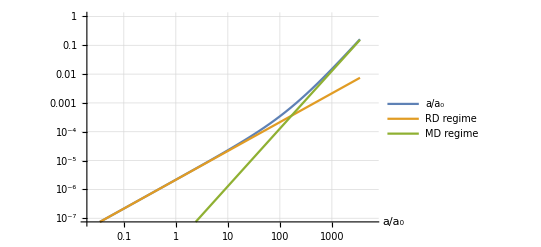

```mathematica
LogLogPlot[{a[η]/a0/.bgsol⟦1⟧,H0 √Ωrad a0 η,1/4 (H0^2 ΩM) a0^2 η^2},{η,η1,η2},Ticks->{Join[Table[10.^i,{i,Round[Log10[a0 η1]],Log10[a0 η2]}],{{ηeq,"η_eq"}}],Automatic},PlotLegends->{"a/a_0","RD regime","MD regime"},AxesLabel->{"a/a_0"},PlotRange->{a[η1]/a0/.bgsol⟦1⟧,1},GridLines->Automatic]
```

## Perturbations

Equations

```mathematica
solvepert[k_,η1_,η2_]:=NDSolve[{
(* Equations *)
-k^2 Φ[η]-3Ha[a[η]]Φ'[η]-3 Ha[a[η]]^2 Φ[η]==(3 H0^2)/2 a[η]^2(ΩM(a0/a[η])^3 δM[η]+Ωrad(a0/a[η])^4 δrad[η]),
δM'[η]-k^2 vM[η]==3Φ'[η],
vM'[η]+Ha[a[η]]vM[η]==-Φ[η],
δrad'[η]-4/3 k^2 vrad[η]==4Φ'[η],
vrad'[η]+1/4 δrad[η]==-Φ[η],
a'[η]/a[η]==Ha[a[η]],
(* Initial conditions *)
a[η1]/a0==H0 a0 η1 √Ωrad,
Φ[η1]==-2/3,
δM[η1]==1,
vM[η1]==1/3 η1,
δrad[η1]==4/3,
vrad[η1]==1/3 η1},
{a,Φ,δM,vM,δrad,vrad},{η,η1,η2}]
```

## Mode entering the horizon deep at MD stage

```mathematica
η1=0.001ηeq
η2=1000ηeq
k1= 10^-3/a0
sol1=solvepert[k1,η1,η2];
```

0.0346481

34648.1

1/1000

```mathematica
ηcross=η/.FindRoot[N[Ha[a[η]]/.sol1[[1]]]==k1,{η,ηeq,η1,η2}][[1]]
```

1919.84

```mathematica
SetOptions[LogLogPlot,Ticks->{Join[Table[10.^i,{i,Round[Log10[a0 η1]],Log10[a0 η2]}],{{a0 ηeq,"η_eq"},{a0 ηcross,"η_×"}}],Automatic},AxesLabel->{"a_0η",Automatic},GridLines->Automatic];
SetOptions[LogLinearPlot,Ticks->{Join[Table[10.^i,{i,Round[Log10[a0 η1]],Log10[a0 η2]}],{{a0 ηeq,"η_eq"},{a0 ηcross,"η_×"}}],Automatic},AxesLabel->{"a_0η",Automatic},GridLines->Automatic];
```

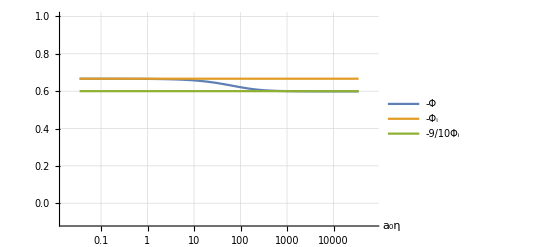

```mathematica
LogLinearPlot[{-Φ[η]/.sol1[[1]],2/3,2/3 9/10},{η,η1,η2},PlotLegends->{"-Φ","-Φ_i","-9/10Φ_i"},PlotRange->{-0.1,1}]
```

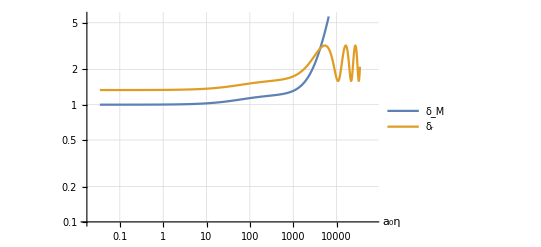

```mathematica
LogLogPlot[{δM[η]/.sol1[[1]],δrad[η]/.sol1[[1]]},{η,η1,η2},
PlotRange->{0.1,Automatic},PlotLegends->{"δ_M","δ_r"}]
```

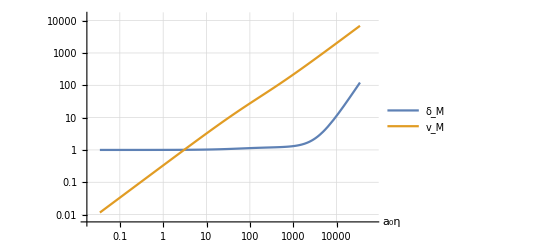

```mathematica
LogLogPlot[{δM[η]/.sol1[[1]],vM[η]/.sol1[[1]]},{η,η1,η2},PlotLegends->{"δ_M","v_M"}]
```

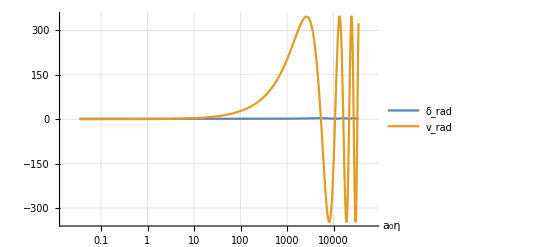

```mathematica
LogLinearPlot[{δrad[η]/.sol1[[1]],vrad[η]/.sol1[[1]]},{η,η1,η2},
PlotLegends->{"δ_rad","v_rad"},PlotRange->All]
```

## Mode entering the horizon deep at RD stage

```mathematica
η1=0.001ηeq
η2=10ηeq
k1= 5/a0
sol1=solvepert[k1,η1,η2];
```

0.0346481

346.481

5

```mathematica
ηcross=η/.FindRoot[N[Ha[a[η]]/.sol1[[1]]]==k1,{η,ηeq,η1,η2}][[1]]
```

0.200246

```mathematica
SetOptions[LogLogPlot,Ticks->{Join[Table[10.^i,{i,Round[Log10[a0 η1]],Log10[a0 η2]}],{{a0 ηeq,"η_eq"},{a0 ηcross,"η_×"}}],Automatic},AxesLabel->{"a_0η",Automatic},GridLines->Automatic];
SetOptions[LogLinearPlot,Ticks->{Join[Table[10.^i,{i,Round[Log10[a0 η1]],Log10[a0 η2]}],{{a0 ηeq,"η_eq"},{a0 ηcross,"η_×"}}],Automatic},AxesLabel->{"a_0η",Automatic},GridLines->Automatic];
```

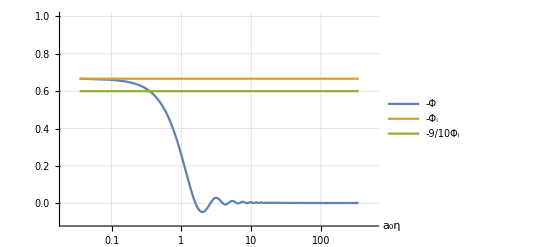

```mathematica
LogLinearPlot[{-Φ[η]/.sol1[[1]],2/3,2/3 9/10},{η,η1,η2},PlotLegends->{"-Φ","-Φ_i","-9/10Φ_i"},PlotRange->{-0.1,1}]
```

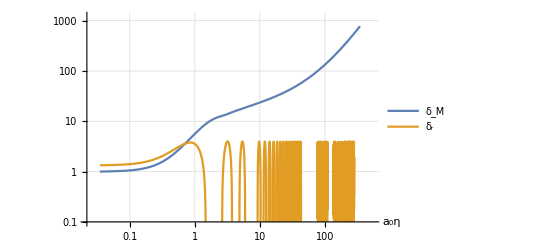

```mathematica
LogLogPlot[{δM[η]/.sol1[[1]],δrad[η]/.sol1[[1]]},{η,η1,η2},
PlotRange->{0.1,Automatic},PlotLegends->{"δ_M","δ_r"}]
```

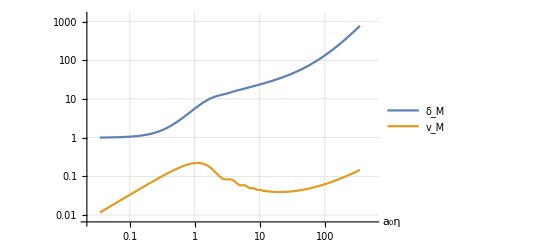

```mathematica
LogLogPlot[{δM[η]/.sol1[[1]],vM[η]/.sol1[[1]]},{η,η1,η2},PlotLegends->{"δ_M","v_M"}]
```

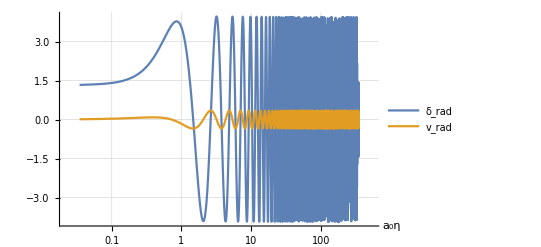

```mathematica
LogLinearPlot[{δrad[η]/.sol1[[1]],vrad[η]/.sol1[[1]]},{η,η1,η2},
PlotLegends->{"δ_rad","v_rad"}]
```